```mathematica
Plot[x,{x,-5,5},PlotRange->Automatic,Aspectratio->Automatic]
```

Plot::optx: Unknown option Aspectratio in Plot[x, {x, -5, 5}, PlotRange → Automatic, Aspectratio → Automatic].

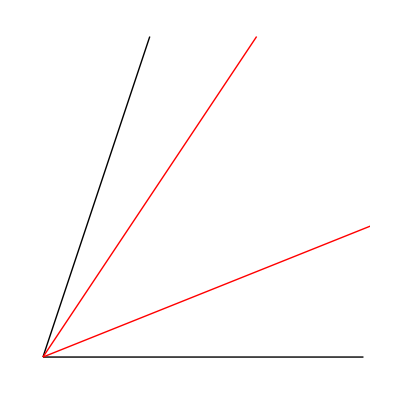

```mathematica
ParametricPlot[{{x,0},{x/3,x},{2x/3,x},{5x/2,x}},{x,0,5},PlotRange->{{-0.10,5},{-0.1,5}},Axes->False,
AspectRatio->Automatic,PlotStyle->{Black,Black,Red,Red}]
```

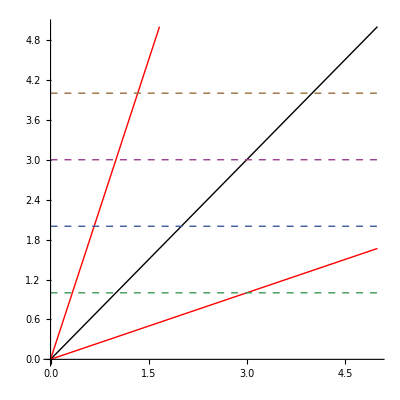

```mathematica
Plot[{x,x/3,3x,1,2,3,4},{x,0,5},PlotRange->{{0,5},{0,5}},AspectRatio->Automatic,PlotStyle->{Black,Red,Red,Dashed,Dashed,Dashed,Dashed}]
```

```mathematica
ParametricPlot[{x,x/3,3x,1,2,3,4},{x,0,5},PlotRange->{{0,5},{0,5}},AspectRatio->Automatic,PlotStyle->{Black,Red,Red,Dashed,Dashed,Dashed,Dashed}]
```

```mathematica
Join[Flatten[Table[{{x,i},{i,x}},{i,4}],1],{x,x/3,3x}]
```

{{x,1},{1,x},{x,2},{2,x},{x,3},{3,x},{x,4},{4,x},x,x/3,3 x}

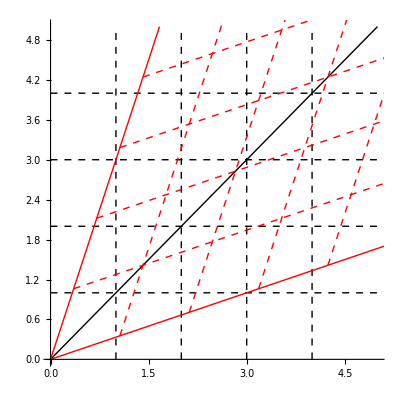

```mathematica
λ=√5/2;v=1/3;γ=1/√(1-1/9);ParametricPlot[Evaluate@Join[Flatten[Table[{{x,i},{i,x}},{i,4}],1],{{x,x},{x/3,x},{3x,x}},Table[{3x+i λ  v/√(1+v^2),x+i λ /√(1+v^2)},{i,4}] ,Table[{x/3+i λ  /√(1+v^2),x+i λ v/√(1+v^2)},{i,4}]  ],{x,0,5},PlotRange->{{0,5},{0,5}},AspectRatio->Automatic,PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},Black,Red,Red,{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red}}]
```

```mathematica
N[γ]
```

1.06066

```mathematica
8/3 1.06
```

2.82667

```mathematica
Joined[Table[{Dashed,Black},{8}],Black,Red,Red,Table[{Dashed,Red},{8}]]
```

Joined[{{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]},{Dashing[{Small,Small}],GrayLevel[0]}},GrayLevel[0],RGBColor[1,0,0],RGBColor[1,0,0],{{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]},{Dashing[{Small,Small}],RGBColor[1,0,0]}}]

```mathematica
Cos[α]//N
```

Cos[Arctan[0.333333]]

```mathematica
ParametricPlot[{{x,1},{x,2},{1,x}},{x,0,5},PlotRange->{{0,5},{0,5}},AspectRatio->Automatic,PlotStyle->{Dashed,Dashed,Dashed}]
```

```mathematica
Flatten[Table[{{x,i},{i,x}},{i,4}],1]
```

{{x,1},{1,x},{x,2},{2,x},{x,3},{3,x},{x,4},{4,x}}